```mathematica
puntos={{865.166,1322.69},{895.482,1355.34},{935.126,1378.66},{972.437,1380.99},{1005.09,1380.99},{1037.73,1399.64},{1063.38,1411.3},{1098.36,1408.97},{1105.36,1392.65},{1126.35,1399.64},{1149.67,1404.31},{1165.99,1392.65},{1189.31,1390.32},{1212.63,1401.98},{1226.62,1432.29},{1245.28,1446.28},{1266.27,1453.28},{1289.59,1446.28},{1317.57,1427.63},{1340.89,1408.97},{1364.21,1387.98},{1389.86,1367.},{1415.51,1353.},{1436.5,1339.01},{1473.81,1339.01},{1511.13,1343.68},{1546.11,1343.68},{1585.75,1343.68},{1620.73,1341.34},{1655.71,1334.35},{1693.02,1322.69},{1728.,1308.7},{1760.65,1287.71}};
```

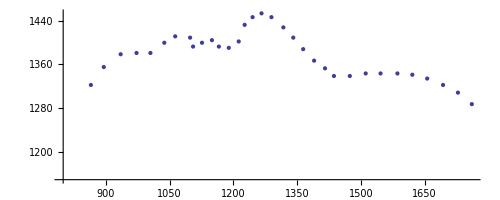

```mathematica
ListPlot[{puntos},AspectRatio->Automatic, AxesOrigin->{800, 1150}]
```

```mathematica
puntos//Dimensions
```

{33,2}

```mathematica
x[j_]:=puntos[[j+1,1]]
```

```mathematica
x[0]
```

865.166

```mathematica
x[32]
```

1760.65

```mathematica
a[j_]:=puntos[[j+1,2]]
```

```mathematica
a[0]
```

1322.69

```mathematica
h[j_]:=x[j+1]-x[j]
```

```mathematica
h[0]
```

30.316

```mathematica
x[1]-x[0]
```

30.316

```mathematica
ListPlot[
Table[{x[i],a[i]},{i,0,Length[puntos]-1}],AspectRatio->Automatic, AxesOrigin->{800, 1150}]
```

-Graphics-

```mathematica
m=({{h[0], 2(h[0]+h[1]), h[1], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, h[1], 2(h[1]+h[2]), h[2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, h[2], 2(h[2]+h[3]), h[3], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, h[3], 2(h[3]+h[4]), h[4], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, h[4], 2(h[4]+h[5]), h[5], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, h[5], 2(h[5]+h[6]), h[6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, h[6], 2(h[6]+h[7]), h[7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, h[7], 2(h[7]+h[8]), h[8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, h[8], 2(h[8]+h[9]), h[9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, h[9], 2(h[9]+h[10]), h[10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[10], 2(h[10]+h[11]), h[11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[11], 2(h[11]+h[12]), h[12], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[12], 2(h[12]+h[13]), h[13], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[13], 2(h[13]+h[14]), h[14], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[14], 2(h[14]+h[15]), h[15], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[15], 2(h[15]+h[16]), h[16], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[16], 2(h[16]+h[17]), h[17], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[17], 2(h[17]+h[18]), h[18], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[18], 2(h[18]+h[19]), h[19], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[19], 2(h[19]+h[20]), h[20], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[20], 2(h[20]+h[21]), h[21], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[21], 2(h[21]+h[22]), h[22], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[22], 2(h[22]+h[23]), h[23], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[23], 2(h[23]+h[24]), h[24], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[24], 2(h[24]+h[25]), h[25], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[25], 2(h[25]+h[26]), h[26], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[26], 2(h[26]+h[27]), h[27], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[27], 2(h[27]+h[28]), h[28], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[28], 2(h[28]+h[29]), h[29], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[29], 2(h[29]+h[30]), h[30], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[30], 2(h[30]+h[31]), h[31]}});
```

```mathematica
h[30]
```

34.98

```mathematica
h[31]
```

32.65

```mathematica
m//Dimensions
```

{31,33}

```mathematica
s=Table[3/h[j-1](a[j-1]-a[j])+3/h[j](a[j+1]-a[j]),{j,1,31}];
```

```mathematica
LinearSolve[m,s]
```

{-0.00160219,-0.00804439,-0.00736852,-0.00333307,0.0169655,-0.012024,0.0193992,-0.10313,0.169398,-0.0365711,-0.0305745,0.0326366,-0.010498,0.0865314,-0.0866704,0.0106406,-0.0226416,-0.00505296,-0.00188319,-0.002842,0.000397715,0.0106737,-0.0112649,0.0197672,-0.00184609,-0.0023195,0.000826015,-0.00106303,-0.00213789,-0.00178619,-0.00013493,-0.00503509,-0.00131831}

```mathematica
c[j_]:=results[[j+1]]
```

```mathematica
c[0]
```

-0.00160219

```mathematica
d[j_]:=(c[j+1]-c[j])/(3 h[j])
```

```mathematica
b[j_]:=1/h[j](a[j+1]-a[j]-h[j]^2/3(2 c[j]+c[j+1]))
```

```mathematica
d[0]
```

-0.0000708339

```mathematica
d[31]
```

0.0000379457

```mathematica
b[0]
```

1.19066

```mathematica
b[31]
```

-0.518934

```mathematica
(** Piecewise **)
```

```mathematica
f[t_]:=Piecewise[Table[{a[i]+b[i](t-x[i])+c[i](t-x[i])^2+d[i](t-x[i])^3,x[i]<t<x[i+1]},{i,0,31}]]
```

```mathematica
f[t]
```

```mathematica
funcion[t_]:=Piecewise[{{1322.69+1.190661652270341 (-865.166+t)-0.0016021899017754498 (-865.166+t)^2-0.00007083392240010603 (-865.166+t)^3, 865.166<t<895.482}, {1355.34+0.8982158305830251 (-895.482+t)-0.008044393476220275 (-895.482+t)^2+5.682828272614262*^-6 (-895.482+t)^3, 895.482<t<935.126}, {1378.66+0.2871861561581787 (-935.126+t)-0.007368523344101716 (-935.126+t)^2+0.00003605236939186522 (-935.126+t)^3, 935.126<t<972.437}, {1380.99-0.11210112298177709 (-972.437+t)-0.0033330734809620625 (-972.437+t)^2+0.0002072145533135614 (-972.437+t)^3, 972.437<t<1005.09}, {1380.99+0.33303709433740963 (-1005.09+t)+0.016965456947081112 (-1005.09+t)^2-0.0002960520040824944 (-1005.09+t)^3, 1005.09<t<1037.73}, {1399.64+0.49432770833717005 (-1037.73+t)-0.01202395529267673 (-1037.73+t)^2+0.00040835758255134883 (-1037.73+t)^3, 1037.73<t<1063.38}, {1411.3+0.6835017266412811 (-1063.38+t)+0.019399160684649676 (-1063.38+t)^2-0.0011676147364189577 (-1063.38+t)^3, 1063.38<t<1098.36}, {1408.97-2.2454145674449792 (-1098.36+t)-0.10313032975515501 (-1098.36+t)^2+0.012977516414336776 (-1098.36+t)^3, 1098.36<t<1105.36}, {1392.65-1.78154427110964 (-1105.36+t)+0.16939751494591732 (-1105.36+t)^2-0.003270900900501161 (-1105.36+t)^3, 1105.36<t<1126.35}, {1399.64+1.0064818688212918 (-1126.35+t)-0.036571114758640874 (-1126.35+t)^2+0.00008571514750062164 (-1126.35+t)^3, 1126.35<t<1149.67}, {1404.31-0.5593534718313015 (-1149.67+t)-0.030574483039497342 (-1149.67+t)^2+0.0012910758884885753 (-1149.67+t)^3, 1149.67<t<1165.99}, {1392.65-0.5256998460739591 (-1165.99+t)+0.032636592460903044 (-1165.99+t)^2-0.0006165610810091605 (-1165.99+t)^3, 1165.99<t<1189.31}, {1390.32-0.009428354160427472 (-1189.31+t)-0.010498020766497702 (-1189.31+t)^2+0.001386927420487176 (-1189.31+t)^3, 1189.31<t<1212.63}, {1401.98+1.763670552595583 (-1212.63+t)+0.08653142157078579 (-1212.63+t)^2-0.004126799477509101 (-1212.63+t)^3, 1212.63<t<1226.62}, {1432.29+1.761726908892118 (-1226.62+t)-0.0866703525002685 (-1226.62+t)^2+0.0017383158084783128 (-1226.62+t)^3, 1226.62<t<1245.28}, {1446.28+0.3430111013498722 (-1245.28+t)+0.010640566458347864 (-1245.28+t)^2-0.0005285405586787287 (-1245.28+t)^3, 1245.28<t<1266.27}, {1453.28+0.09110872468112295 (-1266.27+t)-0.022641632521651696 (-1266.27+t)^2+0.0002514104221105496 (-1266.27+t)^3, 1266.27<t<1289.59}, {1446.28-0.5547291587171922 (-1289.59+t)-0.005052959390797692 (-1289.59+t)^2+0.00003776238173658905 (-1289.59+t)^3, 1289.59<t<1317.57}, {1427.63-0.7488024806695501 (-1317.57+t)-0.0018831850678284051 (-1317.57+t)^2-0.000013705154725715366 (-1317.57+t)^3, 1317.57<t<1340.89}, {1408.97-0.8589937426389975 (-1340.89+t)-0.002841997692439459 (-1340.89+t)^2+0.00004630806957082381 (-1340.89+t)^3, 1340.89<t<1364.21}, {1387.98-0.9159944184142567 (-1364.21+t)+0.0003977148547353662 (-1364.21+t)^2+0.00013354051456426763 (-1364.21+t)^3, 1364.21<t<1389.86}, {1367.-0.6320137187861061 (-1389.86+t)+0.010673657450455705 (-1389.86+t)^2-0.00028510130247814725 (-1389.86+t)^3, 1389.86<t<1415.51}, {1353.-0.6471787766167646 (-1415.51+t)-0.011264887775237802 (-1415.51+t)^2+0.0004928068928507428 (-1415.51+t)^3, 1415.51<t<1436.5}, {1339.01-0.468716035022637 (-1436.5+t)+0.019767162267573486 (-1436.5+t)^2-0.00019309613391529817 (-1436.5+t)^3, 1436.5<t<1473.81}, {1339.01+0.1999192458421087 (-1473.81+t)-0.0018460880015658064 (-1473.81+t)^2-4.228417305905793*^-6 (-1473.81+t)^3, 1473.81<t<1511.13}, {1343.68+0.044459441794673565 (-1511.13+t)-0.002319501603135021 (-1511.13+t)^2+0.000029974429791776317 (-1511.13+t)^3, 1511.13<t<1546.11}, {1343.68-0.0077827175116842295 (-1546.11+t)+0.0008260150592139669 (-1546.11+t)^2-0.000015884967377663715 (-1546.11+t)^3, 1546.11<t<1585.75}, {1343.68-0.017177801923873966 (-1585.75+t)-0.0010630252613378069 (-1585.75+t)^2-0.000010242676626041384 (-1585.75+t)^3, 1585.75<t<1620.73}, {1341.34-0.12914587885714982 (-1620.73+t)-0.0021378917464745903 (-1620.73+t)^2+3.351468939902119*^-6 (-1620.73+t)^3, 1620.73<t<1655.71}, {1334.35-0.2664102092341567 (-1655.71+t)-0.0017861885959212617 (-1655.71+t)^2+0.00001475260175137744 (-1655.71+t)^3, 1655.71<t<1693.02}, {1322.69-0.33808713964127984 (-1693.02+t)-0.0001349298818895873 (-1693.02+t)^2-0.000046694850346035154 (-1693.02+t)^3, 1693.02<t<1728.}, {1308.7-0.5189343468623221 (-1728.+t)-0.005035087477202519 (-1728.+t)^2+0.00003794566539155574 (-1728.+t)^3, 1728.<t<1760.65}, {0, True}}]
```

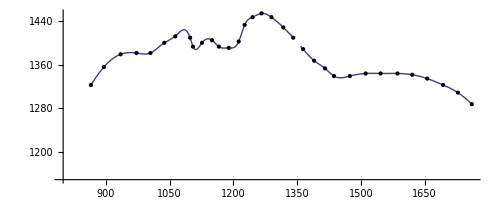

```mathematica
Plot[funcion[t],{t,x[0],x[32]},AspectRatio->Automatic,AxesOrigin->{800,1150},Epilog->Map[Point,puntos]]
```

```mathematica
NIntegrate[funcion[t],{t,x[0],x[32]}]
```

1.2294×10^6

```mathematica
f1[t_]:=Pi*(f[t])^2
```

```mathematica
NIntegrate[f1[t],{t,x[0],x[32]}]
```

5.30686×10^9